The file format for the file is a list of points with seven entries each. The entries contain the following:

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in %, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

 9) Bsgamma ect
 
 10) {{Δa_e, Δa_μ, Δa_τ},
 {d_e, d_μ, d_τ}, 
 {BR( τ -> μ γ ), BR( τ -> e γ ), BR( μ -> e γ ) }}

```mathematica
91/0.23
```

395.652

```mathematica
file1=<<"/Users/ruppell/Math/temp/output-cpx-new-edm_clean.txt";
label1="Fig CPV";
```

```mathematica
snuLSP[name_]:=Select[name,#[[3,5,1]]<Abs@#[[3,1,1]]&];
χ0LSP[name_]:=Select[name,#[[3,5,1]]>Abs@#[[3,1,1]]&];
χ0plus[name_]:=Select[name,#[[3,1,1]]>0&];
χ0sing[name_]:=Select[name,#[[3,1,1]]<0&];
χ0sing[name_]:=Select[name,Power[Abs@(#[[4,1,1,5]]+I #[[4,1,2,5]]),2]>0.97&];
snuLeft[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2<0.99&];
snuRight[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2>0.99&];
selSnuMass[down_,up_][name_]:=Select[name,(#[[3,5,1]]<up&&#[[3,5,1]]>down)&];
selHiggsMass[down_,up_][name_]:=Select[name,Or@@((#<up&&#>down)&/@#[[3,6,{2,3,4,5,6}]])&];
```

```mathematica
p1=Show[
ListLogPlot[
Transpose@{(χ0LSP@#)[[;;,3,5,1]],(χ0LSP@#)[[;;,6,1]]},
AxesLabel->{"M_snu","Ωh^2"},
ImageSize->400,
PlotRange->{{0,500},{0.0001,1}},
PlotLabel->"CP violating - χ0 LSP",
Epilog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
]&;
p2=Show[
ListLogPlot[
{Transpose@{(snuLeft@snuLSP@#)[[;;,3,5,1]],(snuLeft@snuLSP@#)[[;;,6,1]]},
Transpose@{(snuRight@snuLSP@#)[[;;,3,5,1]],(snuRight@snuLSP@#)[[;;,6,1]]}},
AxesLabel->{"M_snu","Ωh^2"},
ImageSize->400,
PlotRange->{{0,500},{0.0001,1}},
PlotLabel->"CP violating - snu LSP",
Epilog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
]&;
p3=Show[
ListLogPlot[
{Transpose@{(χ0LSP@h1@cuts@#)[[;;,3,5,1]],(χ0LSP@h1@cuts@#)[[;;,6,1]]},Transpose@{(χ0LSP@h23@cuts@#)[[;;,3,5,1]],(χ0LSP@h23@cuts@#)[[;;,6,1]]}},
AxesLabel->{"M_snu","Ωh^2"},
ImageSize->400,
PlotRange->{{0,500},{0.0001,1}},
PlotStyle->PointSize[0.02],
PlotLabel->"CP violating - χ0 LSP - cuts",
Epilog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
]&;
p4=Show[
ListLogPlot[
{Transpose@{(snuLSP@h1@cuts@#)[[;;,3,5,1]],(snuLSP@h1@cuts@#)[[;;,6,1]]},
Transpose@{(snuLSP@h23@cuts@#)[[;;,3,5,1]],(snuLSP@h23@cuts@#)[[;;,6,1]]}},
AxesLabel->{"M_snu","Ωh^2"},
ImageSize->400,
PlotRange->{{0,500},{0.0001,1}},
PlotStyle->PointSize[0.02],
PlotLabel->"CP violating - snu LSP - cuts",
Epilog->{Opacity[0.5,Brown],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
]&;
```

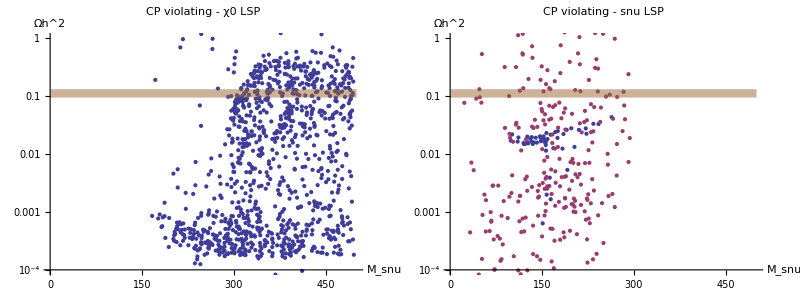

```mathematica
TableForm@{{p1@file1,p2@file1}}
```

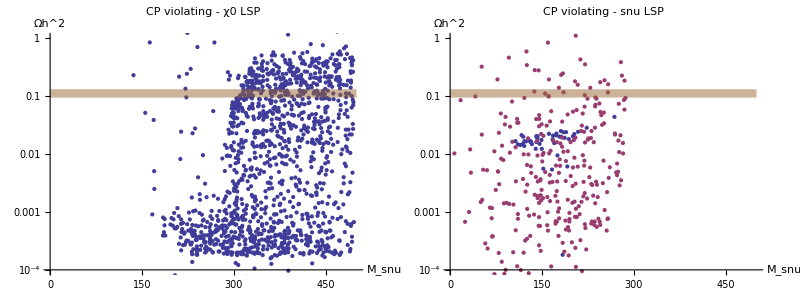

```mathematica
TableForm@{{p1,p2}}
```

```mathematica
bsg[name_]:=Select[name,(#[[9,1]]<4.97*^-4&&#[[9,1]]>2.13*^-4)&];
ΔMd[name_]:=Select[name,(#[[9,2]]<5.15*^-1&&#[[9,2]]>4.99*^-1)&];
ΔMs[name_]:=Select[name,(#[[9,3]]<1.753*^1&&#[[9,3]]>1.801*^1)&];
bsμμ[name_]:=Select[name,(#[[9,4]]<1.1*^-8)&];
bτν[name_]:=Select[name,(#[[9,5]]<2.45*^-4&&#[[9,5]]>8.9*^-5)&];
```

```mathematica
dϵ[name_]:=Select[name,(#[[10,2,1]]<1.43*^-27&&#[[10,2,1]]>-0.5*^-28)&];
dμ[name_]:=Select[name,(#[[10,2,2]]<0.8*^-19)&];
BRτμγ[name_]:=Select[name,(#[[10,3,1]]<4.4*^-8)&];
BRτϵγ[name_]:=Select[name,(#[[10,3,2]]<3.3*^-8)&];
BRμϵγ[name_]:=Select[name,(#[[10,3,3]]<1.2*^-11)&];
```

```mathematica
pName={"M1","M2","M3","M0","Mtau","MQ","MNR","tanβ","v","vevS","Atop","Abtm","Atau","An11","An12","An13","AlambdaN","Yn11","Yn12","Yn13","lambda","lambdaN","kappa","PhisPI","Phi2PI","ksi","Alambda","Akappa","mh1","mh2","mS"};
```

```mathematica
pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]
```

{M0,MNR,tanβ,vevS,AlambdaN,lambda,lambdaN,kappa,PhisPI,Phi2PI,ksi,Alambda,Akappa,mh1,mh2,mS}

```mathematica
TableForm@
{pName[[{4,7,10,17,26}]],
Histogram@file1[[;;,2,#]]&/@{4,7,10,17,26},
Histogram@(bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{4,7,10,17,26},
Histogram@(BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{4,7,10,17,26}}
```

```mathematica
TableForm@
{pName[[{8,21,22,23,24,25}]],
Histogram@file1[[;;,2,#]]&/@{8,21,22,23,24,25},
Histogram@(bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{8,21,22,23,24,25},
Histogram@(BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{8,21,22,23,24,25}}
```

```mathematica
TableForm@
{pName[[{27,28,29,30,31}]],
Histogram@Abs@file1[[;;,2,#]]&/@{27,28,29,30,31},
Histogram@Abs@(bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{27,28,29,30,31},
Histogram@Abs@(BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@file1)[[;;,2,#]]&/@{27,28,29,30,31}}
```

```mathematica
N@First@Dimensions@bτν@bsμμ@bsg@file1/First@Dimensions@file1
```

0.951598

```mathematica
N@First@Dimensions@BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@file1/First@Dimensions@file1
```

0.0408835

```mathematica
cuts=BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@#&;
h1[name_]:=Select[name,(#[[3,6,2]]<128&&#[[3,6,2]]>123)&];
h23[name_]:=Select[name,((#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
h123[name_]:=Select[name,((#[[3,6,2]]<128&&#[[3,6,2]]>123)||(#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
dm[name_]:=Select[name,(#[[6,1]]<0.1311&&#[[6,1]]>0.0941)&];
dmup[limU_,limD_][name_]:=Select[name,(#[[6,1]]<limU&&#[[6,1]]>limD)&];
```

```mathematica
lep=-Graphics-;
```

```mathematica
gHZZ[i_,name_]:=Sin@ArcTan@name[[;;,2,8]] (name[[;;,4,9,i,2]]+I name[[;;,4,9,i,5]])/Sqrt@2+
Cos@ArcTan@name[[;;,2,8]](name[[;;,4,9,1,i]]+I name[[;;,4,9,4,i]])/Sqrt@2;
xi0[name_]:=Power[Abs@gHZZ[1,name],2];
xi1[name_]:=Power[Abs@gHZZ[2,name],2];
xi2[name_]:=Power[Abs@gHZZ[3,name],2];
xi3[name_]:=Power[Abs@gHZZ[4,name],2];
xi4[name_]:=Power[Abs@gHZZ[5,name],2];
xi5[name_]:=Power[Abs@gHZZ[6,name],2];
```

```mathematica
plotXiT=ListPlot[
{Transpose@{#[[;;,3,6,2]],Log[10,xi1[#]]},
Transpose@{#[[;;,3,6,3]],Log[10,xi2[#]]}},
PlotRange->{{12,120},{0,-2}},
AxesOrigin->{12,-2},
AspectRatio->0.96,
ImageSize->350,
ImagePadding->{{76,17},{27,0}},
Axes->False
]&;
```

```mathematica
img=ImageCompose[lep,plotXiT[#]]&;
```

```mathematica
TableForm@{{img@file1,img@cuts@file1}}
```

-Graphics- | -Graphics-

```mathematica
plot6=ListPlot[
Transpose@{Log[10,#1[[;;,6,1]]],Log[10,Abs@#1[[;;,##2]]]},
AxesOrigin->{-5,-24.5},
AspectRatio->1,
ImageSize->400,
PlotRange->{{0,-5},{-24.5,-28}},
Prolog->{
{Opacity[0.5,LightBrown],Rectangle[{10~Log~0.0941,-24.5},{10~Log~0.1311,-28}]},
{Opacity[0.5,LightBrown],Rectangle[{-5,10~Log~14.3*^-28},{0,-28}]},
{Thin,Line@{{-5,10~Log~14.3*^-28},{0,10~Log~14.3*^-28}}},
{Thin,Line@{{10~Log~0.0941,-24.5},{10~Log~0.0941,-28}}},
{Thin,Line@{{10~Log~0.1311,-24.5},{10~Log~0.1311,-28}}}}
]&[#,10,2,1]&;
```

```mathematica
TableForm@{{plot6@file1,plot6@cuts@file1}}
```

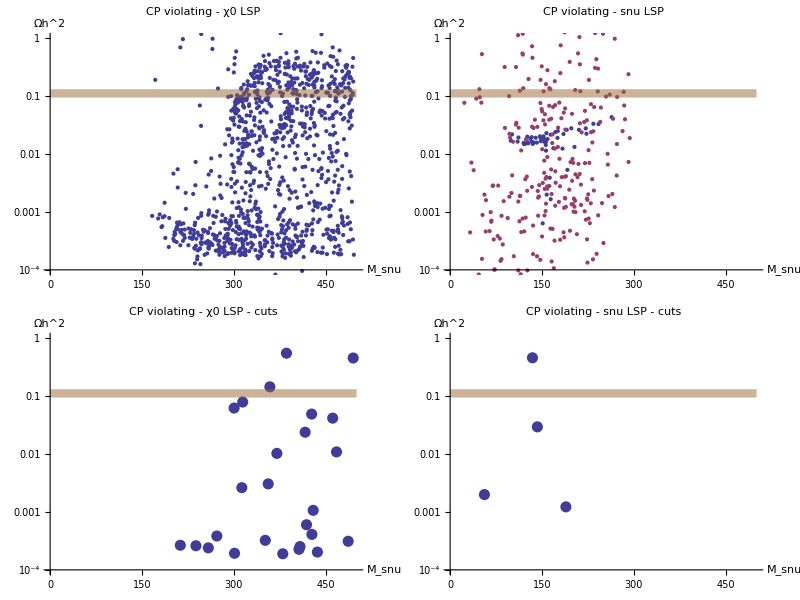

```mathematica
TableForm@{{p1@file1,p2@file1},{p3@file1,p4@file1}}
```

```mathematica
{{"Spectrum","gHZZ","RD","Channels","DM -- Nucleon", "bsgamma et al", "edm et al"}}~Join~(χ0LSP@dm@cuts@file1)[[;;,{3,5,6,7,8,9,10}]]//TableForm
```

Spectrum | gHZZ | RD | Channels | DM -- Nucleon | bsgamma et al | edm et al
293.484 | -418.921 | 422.016 | 621.329 | -986.746 |  |  | 
412.606 | 621.017 |  |  |  |  |  | 
0 | 1553.52 |  |  |  |  |  | 
0 | 4.163×10^-12 | 1.95008×10^-10 | -465.864 |  |  |  | 
339.912 | 339.912 | 339.912 | 339.912 | 339.912 | 339.912 | 486.31 | 562.821
-1.11496×10^-9 | 33.7358 | 126.162 | 1522.6 | 1558.09 | 1559.78 |  | 
342.598 | 348.771 | 348.771 | 349.221 | 349.221 | 355.288 |  | 
998.556 | 999.357 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
813.981 | 1180.33 |  |  |  |  |  | 
986.959 | 1014.95 |  |  |  |  |  |  | 0.499941 |  | 
0.00288212 |  | 
0.493388 |  | 
0.00190992 |  | 
0.00166514 |  | 
0.00021446 |  | 
0.00002921 | 2.39756×10^-7 | 0.00125795 | 0.103613
~o1
24.9845 | 0.0000326 | ~n1 ~n1 | s S
0.0573 | ~n1 ~n1 | b B
0.00246 | ~n1 ~n1 | c C
0.00218 | ~n1 ~n1 | e2 E2
0.607 | ~n1 ~n1 | e3 E3
0.0266 | ~n1 ~n1 | h1 h1
59.2 | ~n1 ~n1 | h2 h2
0 | ~n1 ~n1 | n4 n4
0 | ~n1 ~n1 | N4 N4
506 | ~n1 ~n1 | W+ W-
443 | ~n1 ~n1 | Z Z
3.12 | ~o1 ~o1 | b B
0.104 | ~o1 ~o1 | h1 h1
0.276 | ~o1 ~o1 | h2 h2
42.5 | ~o1 ~o1 | W+ W-
5.04 | ~o1 ~o1 | Z Z | -5.98588×10^-9 | -5.98588×10^-9 | -1.10774×10^-7 | -1.10774×10^-7
-6.20484×10^-9 | -6.20484×10^-9 | 1.03099×10^-7 | 1.03099×10^-7
1.55631×10^-8 | 1.55631×10^-8 | 0.0000159895 | 0.0000159895
1.67225×10^-8 | 1.67225×10^-8 | 0.0000138506 | 0.0000138506 | 0.000405619
0.59557
20.6355
3.56059×10^-9
0.00013145
1.7199×10^-9 | -1.98577×10^-15 | -8.49001×10^-11 | -6.0763×10^-10
9.03437×10^-28 | 1.86804×10^-25 | -2.44805×10^-23
1.01452×10^-20 | 1.30393×10^-20 | 2.52607×10^-19

```mathematica
{pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]}~Join~(χ0LSP@dm@cuts@file1)[[;;,2,{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]//TableForm
```

M0 | MNR | tanβ | vevS | AlambdaN | lambda | lambdaN | kappa | PhisPI | Phi2PI | ksi | Alambda | Akappa | mh1 | mh2 | mS
345.994 | 244.137 | 26.8119 | 638.561 | 414.941 | 0.669993 | 0.364776 | 0.758933 | 3.17836 | 2.8485 | 873.163 | 684.69 | -706.797 | 1496.75 | 0.+391.59 ⅈ | 466.651

```mathematica
{{"Spectrum","gHZZ","RD","Channels","DM -- Nucleon", "bsgamma et al", "edm et al"}}~Join~(snuLSP@dm@cuts@file1)[[;;,{3,5,6,7,8,9,10}]]//TableForm
```

Spectrum | gHZZ | RD | Channels | DM -- Nucleon | bsgamma et al | edm et al
296.034 | 457.107 | -467.906 | 623.583 | -1205.25 |  |  | 
452.285 | 623.327 |  |  |  |  |  | 
0 | 3804.43 |  |  |  |  |  | 
-2.167×10^-12 | 0 | 2.18435×10^-9 | -41.5508 |  |  |  | 
257.42 | 270.796 | 270.796 | 270.796 | 270.796 | 270.796 | 270.796 | 362.573
-0.0000431584 | 5.19866 | 124.626 | 1201.13 | 3804.03 | 3804.13 |  | 
274.176 | 281.851 | 281.851 | 282.408 | 282.408 | 289.876 |  | 
998.554 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.77 |  |  |  |  |  | 
811.861 | 1181.79 |  |  |  |  |  | 
967.637 | 1033.39 |  |  |  |  |  |  | 0.498521 |  | 
0.000409806 |  | 
0.497876 |  | 
0.0017134 |  | 
0.00147893 |  | 
1.5075×10^-6 |  | 
0.00073901 | 3.14092×10^-6 | 5.87485×10^-7 | 0.115513
~n1
26.7727 | 7.26×10^-7 | ~n1 ~n1 | s S
0.00127 | ~n1 ~n1 | b B
0.0000595 | ~n1 ~n1 | c C
2.7×10^-7 | ~n1 ~n1 | e2 E2
0.0000764 | ~n1 ~n1 | e3 E3
18.2 | ~n1 ~n1 | h1 h1
0.652 | ~n1 ~n1 | h2 h2
0.0104 | ~n1 ~n1 | n4 n4
0.0104 | ~n1 ~n1 | N4 N4
1.37 | ~n1 ~n1 | W+ W-
0.655 | ~n1 ~n1 | Z Z
0.776 | ~o1 ~o1 | b B
0.0249 | ~o1 ~o1 | h1 h1
0.0545 | ~o1 ~o1 | h2 h2
14.7 | ~o1 ~o1 | W+ W-
0.0778 | ~o1 ~o1 | Z Z | -1.81072×10^-8 | -1.81072×10^-8 | 0 | 0
-1.83403×10^-8 | -1.83403×10^-8 | 0 | 0
1.42283×10^-7 | 1.42283×10^-7 | 0 | 0
1.4597×10^-7 | 1.4597×10^-7 | 0 | 0 | 0.000431114
0.595112
20.6238
3.74318×10^-9
0.000130468
2.86066×10^-9 | 1.52347×10^-15 | 6.51346×10^-11 | 6.13858×10^-8
1.14854×10^-27 | 2.37486×10^-25 | -1.57467×10^-22
3.07742×10^-20 | 4.71461×10^-21 | 1.26855×10^-18

```mathematica
{pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]}~Join~(snuLSP@dm@cuts@file1)[[;;,2,{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]//TableForm
```

M0 | MNR | tanβ | vevS | AlambdaN | lambda | lambdaN | kappa | PhisPI | Phi2PI | ksi | Alambda | Akappa | mh1 | mh2 | mS
278.403 | 311.666 | 36.7273 | 842.341 | -188.559 | 0.557125 | 0.0246639 | 0.710076 | 3.19186 | 0.0570452 | 170.971 | -243.241 | -3.79057 | 3777.51 | 0.+428.033 ⅈ | 0.+848.788 ⅈ